# Plotting projected (electronic) DOS from different DFT codes for Spin-polarized systems

The notebook can read spin-polarized PDOS from different DFT codes (VASP, FHI - AIMS and CP2K) and plot them in the same way. For VASP also polarization in case of spin-orbit coupling can be plotted.
In the second part (VIEW) there is possibility to visualize the amount of PDOS per atom in 3 D balls & sticks model.

```mathematica
(* a way to lower down the amount of memory *)
$HistoryLength=2;
```

```mathematica
(* for path checking *)
atomicprop=Import[NotebookDirectory[]<>"/atomic_prop.dat","Table"];
path="~/Documents/WORK/PDOS_test_CP2K_2_sp/";
geom=Import[path<>"input.xyz","Table"]; (*Not necessary, but good for checking; eg. "geometry.in" for FHI-AIMS; "CONTCAR" for VASP; "???.xyz" is working for others ...*)  
(*maxat1=geom[[1,1]]*) (* This is not neccessary for plotting *)
geom[[Range[1,20],All]]//TableForm  (* Just to show sample*)
```

51 |  |  |  | 
Lattice="19.014 0.0 0.0 9.507 16.4666070276 0.0 7.54627357635e-16 4.35684308068e-16 12.324" | Properties=species:S:1:pos:R:3:Z:I:1 | pbc="F F F" |  | 
Mo | 1.585 | 0.915 | 3.081 | 42
S | 3.169 | 1.83 | 1.516 | 16
S | 3.169 | 1.83 | 4.646 | 16
Mo | 3.1695 | 3.65943 | 3.081 | 42
S | 4.7535 | 4.57443 | 1.516 | 16
S | 4.7535 | 4.57443 | 4.646 | 16
Mo | 4.754 | 6.40387 | 3.081 | 42
S | 6.338 | 7.31887 | 1.516 | 16
S | 6.338 | 7.31887 | 4.646 | 16
Mo | 6.3385 | 9.1483 | 3.081 | 42
S | 7.9225 | 10.0633 | 1.516 | 16
S | 7.9225 | 10.0633 | 4.646 | 16
Mo | 7.923 | 11.8927 | 3.081 | 42
S | 9.507 | 12.8077 | 1.516 | 16
S | 9.507 | 12.8077 | 4.646 | 16
Mo | 9.5075 | 14.6372 | 3.081 | 42
Mo | 4.754 | 0.915 | 3.081 | 42
S | 6.338 | 1.83 | 1.516 | 16

## VAPS spin-polarized

4 cells with uploading the PDOS: Sometimes different summing for doses-up&down has to be used, depending on format (LORBIT=10 or 11) and depending on amount of orbitals -- use un/comment relevant lines
5th cell is for possible rescaling of PDOS to number of atoms

```mathematica
list=Table[i,{i,1,2,1}];
pathse=path(*"~/Documents/WORK/z-sshfs/Tarkil/CuPc_SnSi/PBE+U_VASP/"*);doscar1=Import[pathse<>"DOSCAR","Table"];
(*doscar1[[Range[1,7]]]*)noat=doscar1[[1,1]];nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
(*For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];*)(* spd division only LORBIT=10*)
For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];(* spdf division only LORBIT=10*)
(*For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];*)(* spxpy... division - LORBIT = 11*)
dosesmolup=Array[Null,{nosteps,2}];
dosesmolup[[All,1]]=dostot[[All,1]];
dosesmoldn=Array[Null,{nosteps,2}];
dosesmoldn[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmolup[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolup[[i,2]]=dosesmolup[[i,2]]+dosesup[list[[j]]][[i,2]]],dosesmoldn[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmoldn[[i,2]]=dosesmoldn[[i,2]]+dosesdn[list[[j]]][[i,2]]]}];
dosesmolup2=Inner[Plus,dosesmolup,{-fermi+0,0},List];
dosesmoldn2=Inner[Plus,dosesmoldn,{-fermi+0,0},List];
dosesmolup2[[1,2]]=dosesmolup2[[2,2]]; (* 1st energy is always wrong *)
dosesmoldn2[[1,2]]=dosesmoldn2[[2,2]];na1=Length[list]; (* number of atoms, for rescalling, if necessary *)
dosup1=dosesmolup2;dosdn1=dosesmoldn2;
```

-0.774192

```mathematica
list=Table[i,{i,2+1,2+32+12,1}];
pathse=path;(*"~/Documents/WORK/z-sshfs/Tarkil/CuPc_SnSi/4L_VASP/1Si_SnSi_CuPc_2/";*)doscar1=Import[pathse<>"DOSCAR","Table"];
(*doscar1[[Range[1,7]]]*)noat=doscar1[[1,1]];nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
(*For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];*)(* spd division only LORBIT=10*)
For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];(* spdf division only LORBIT=10*)
(*For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];*)(* spxpy... division - LORBIT = 11*)
dosesmolup=Array[Null,{nosteps,2}];
dosesmolup[[All,1]]=dostot[[All,1]];
dosesmoldn=Array[Null,{nosteps,2}];
dosesmoldn[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmolup[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolup[[i,2]]=dosesmolup[[i,2]]+dosesup[list[[j]]][[i,2]]],dosesmoldn[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmoldn[[i,2]]=dosesmoldn[[i,2]]+dosesdn[list[[j]]][[i,2]]]}];
dosesmolup2=Inner[Plus,dosesmolup,{-fermi+0,0},List];
dosesmoldn2=Inner[Plus,dosesmoldn,{-fermi+0,0},List];
dosesmolup2[[1,2]]=dosesmolup2[[2,2]]; (* 1st energy is always wrong *)
dosesmoldn2[[1,2]]=dosesmoldn2[[2,2]];na2=Length[list]; (* number of atoms, for rescalling, if necessary *)
dosup2=dosesmolup2;dosdn2=dosesmoldn2;
```

-0.774192

```mathematica
list=Table[i,{i,2+32+12+1,2+32+12+125,1}];
pathse=path(*"~/Documents/WORK/z-sshfs/Tarkil/CuPc_SnSi/4L_VASP/1Si_SnSi_CuPc_3/"*);doscar1=Import[pathse<>"DOSCAR","Table"];
(*doscar1[[Range[1,7]]]*)noat=doscar1[[1,1]];nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
(*For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];*)(* spd division only LORBIT=10*)
For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];(* spdf division only LORBIT=10*)
(*For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];*)(* spxpy... division - LORBIT = 11*)
dosesmolup[[All,1]]=dostot[[All,1]];
dosesmoldn=Array[Null,{nosteps,2}];
dosesmoldn[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmolup[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolup[[i,2]]=dosesmolup[[i,2]]+dosesup[list[[j]]][[i,2]]],dosesmoldn[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmoldn[[i,2]]=dosesmoldn[[i,2]]+dosesdn[list[[j]]][[i,2]]]}];
dosesmolup2=Inner[Plus,dosesmolup,{-fermi+0,0},List];
dosesmoldn2=Inner[Plus,dosesmoldn,{-fermi+0,0},List];
dosesmolup2[[1,2]]=dosesmolup2[[2,2]]; (* 1st energy is always wrong *)
dosesmoldn2[[1,2]]=dosesmoldn2[[2,2]];na3=Length[list]; (* number of atoms, for rescalling, if necessary *)
dosup3=dosesmolup2;dosdn3=dosesmoldn2;
```

-0.774192

```mathematica
list=Table[i,{i,1,57,1}];
pathse=(*path*)"~/Documents/WORK/z-sshfs/Tarkil/CuPc_SnSi/4L_VASP/1Si_SnSi_CuPc_Pavel/";doscar1=Import[pathse<>"DOSCAR","Table"];
(*doscar1[[Range[1,7]]]*)noat=doscar1[[1,1]];nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
(*For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];*)(* spd division only LORBIT=10*)
For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];(* spdf division only LORBIT=10*)
(*For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];*)(* spxpy... division - LORBIT = 11*)
dosesmolup=Array[Null,{nosteps,2}];
dosesmolup[[All,1]]=dostot[[All,1]];
dosesmoldn=Array[Null,{nosteps,2}];
dosesmoldn[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmolup[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolup[[i,2]]=dosesmolup[[i,2]]+dosesup[list[[j]]][[i,2]]],dosesmoldn[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmoldn[[i,2]]=dosesmoldn[[i,2]]+dosesdn[list[[j]]][[i,2]]]}];
dosesmolup2=Inner[Plus,dosesmolup,{-fermi+0,0},List];
dosesmoldn2=Inner[Plus,dosesmoldn,{-fermi+0,0},List];
dosesmolup2[[1,2]]=dosesmolup2[[2,2]]; (* 1st energy is always wrong *)
dosesmoldn2[[1,2]]=dosesmoldn2[[2,2]];na4=Length[list]; (* number of atoms, for rescalling, if necessary *)
dosup4=dosesmolup2;dosdn4=dosesmoldn2;
```

-1.18723

```mathematica
(*rescalling of the PDOS per amount of atoms *)
dosup1[[All,2]]*=1/na1;
dosdn1[[All,2]]*=1/na1;

dosup2[[All,2]]*=1/na2;
dosdn2[[All,2]]*=1/na2;

dosup3[[All,2]]*=1/na3;
dosdn3[[All,2]]*=1/na3;

(*dosup4[[All,2]]*=1/na4;
dosdn4[[All,2]]*=1/na4;*)
```

## FHI-AIMS spin-polarized

```mathematica
shift=0.0;

list=Table[i,{i,1,57,1}];na4=Length[list]; (* number of atoms, for rescalling, if necessary *)
j=2;  (* All orbitals: j=2; s-orb.08: j=3; p-orb: j=4; d-orb: j=5;*)
path0=path; (*"~/Documents/WORK/z-sshfs/Tarkil/FePc_Gr/B3LYP_light_triplet_opt/";*)
tmp1=Import[path0<>"geometry.in","Table"];bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];tmp1=.; (* possible error: Part::partw: "Part [i,1] of ... does not exist.", it has no effect on functionality*)
tmp2=Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosdn1=tmp2[[All,{1,2}]];
tmp2=.;dosdn1[[All,2]]=0.0;null=Table[0.0,{i,Length[dosdn1]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}]
dosdn1[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dd[i]=.},{i,list}];
dosdn1[[All,2]]*=-1;
dosdn1=Inner[Plus,dosdn1,{shift,0},List];na1=Length[list]; <(* number of atoms, for rescalling, if necessary *)

tmp2=Import[path0<>"atom_proj_dos_spin_up"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosup1=tmp2[[All,{1,2}]];
tmp2=.;dosup1[[All,2]]=0.0;null=Table[0.0,{i,Length[dosdn1]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}];dosup1[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dd[i]=.},{i,list}];
dosup1=Inner[Plus,dosup1,{shift,0},List];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
shift=0.0;

list=(*Table[i,{i,1,57,1}]*){1};na2=Length[list]; (* number of atoms, for rescalling, if necessary *)
j=5;  (* All orbitals: j=2; s-orb.08: j=3; p-orb: j=4; d-orb: j=5;*)
path0=path; (*"~/Documents/WORK/z-sshfs/Tarkil/FePc_Gr/B3LYP_light_triplet_opt/";*)
tmp1=Import[path0<>"geometry.in","Table"];bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];tmp1=.; (* possible error: Part::partw: "Part [i,1] of ... does not exist.", it has no effect on functionality*)
tmp2=Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosdn2=tmp2[[All,{1,2}]];
tmp2=.;dosdn2[[All,2]]=0.0;null=Table[0.0,{i,Length[dosdn2]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}]
dosdn2[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dd[i]=.},{i,list}];
dosdn2[[All,2]]*=-1;
dosdn2=Inner[Plus,dosdn2,{shift,0},List];

tmp2=Import[path0<>"atom_proj_dos_spin_up"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosup2=tmp2[[All,{1,2}]];
tmp2=.;dosup2[[All,2]]=0.0;null=Table[0.0,{i,Length[dosup2]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}];dosup2[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dd[i]=.},{i,list}];
dosup2=Inner[Plus,dosup2,{shift,0},List];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
shift=0.0;

list=(*Table[i,{i,1,57,1}]*){1};na3=Length[list]; (* number of atoms, for rescalling, if necessary *)
j=2;  (* All orbitals: j=2; s-orb.08: j=3; p-orb: j=4; d-orb: j=5;*)
path0=path; (*"~/Documents/WORK/z-sshfs/Tarkil/FePc_Gr/B3LYP_light_triplet_opt/";*)
tmp1=Import[path0<>"geometry.in","Table"];bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];tmp1=.; (* possible error: Part::partw: "Part [i,1] of ... does not exist.", it has no effect on functionality*)
tmp2=Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosdn3=tmp2[[All,{1,2}]];
tmp2=.;dosdn3[[All,2]]=0.0;null=Table[0.0,{i,Length[dosdn3]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}]
dosdn3[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dd[i]=.},{i,list}];
dosdn3[[All,2]]*=-1;
dosdn3=Inner[Plus,dosdn3,{shift,0},List];

tmp2=Import[path0<>"atom_proj_dos_spin_up"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosup3=tmp2[[All,{1,2}]];
tmp2=.;dosup3[[All,2]]=0.0;null=Table[0.0,{i,Length[dosup3]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}];dosup3[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dd[i]=.},{i,list}];
dosup3=Inner[Plus,dosup3,{shift,0},List];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
shift=0.0;

list=(*Table[i,{i,1,57,1}]*){1};na4=Length[list]; (* number of atoms, for rescalling, if necessary *)
j=4;  (* All orbitals: j=2; s-orb.08: j=3; p-orb: j=4; d-orb: j=5;*)
path0=path; (*"~/Documents/WORK/z-sshfs/Tarkil/FePc_Gr/B3LYP_light_triplet_opt/";*)
tmp1=Import[path0<>"geometry.in","Table"];bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];tmp1=.; (* possible error: Part::partw: "Part [i,1] of ... does not exist.", it has no effect on functionality*)
tmp2=Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosdn4=tmp2[[All,{1,2}]];
tmp2=.;dosdn4[[All,2]]=0.0;null=Table[0.0,{i,Length[dosdn4]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}]
dosdn4[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dd[i]=.},{i,list}];
dosdn4[[All,2]]*=-1;
dosdn4=Inner[Plus,dosdn4,{shift,0},List];

tmp2=Import[path0<>"atom_proj_dos_spin_up"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosup4=tmp2[[All,{1,2}]];
tmp2=.;dosup4[[All,2]]=0.0;null=Table[0.0,{i,Length[dosup4]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}];dosup4[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dd[i]=.},{i,list}];
dosup4=Inner[Plus,dosup4,{shift,0},List];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
(*rescalling of the PDOS per amount of atoms *)
dosup1[[All,2]]*=1/na1;
dosdn1[[All,2]]*=1/na1;

dosup2[[All,2]]*=1/na2;
dosdn2[[All,2]]*=1/na2;

dosup3[[All,2]]*=1/na3;
dosdn3[[All,2]]*=1/na3;

(*dosup4[[All,2]]*=1/na4;
dosdn4[[All,2]]*=1/na4;*)
```

## CP2K spin-polarized

```mathematica
(* For preparation - it is important to add &PDOS // NLUMO-1 // COMPONENTS.TRUE. // FILENAME dosfile// LOG_PRINT_KEY TRUE // to_be_added // &END PDOS into PRINT in DFT part of the input file - to_be_added can be prepared using this cell; Adjust following line:*)
minatom=1; maxatom=51; components=True; (* add even angular components - px, py ...; normally (False) on s, p, ...; Next lines are automatic *)
tobeadded=Flatten[Table[If[components,{{"","","&LDOS"},{"","","  COMPONENTS",".TRUE."},{"","","  LIST",i},{"","","&END LDOS"}},
{{"","","&LDOS"},{"","","  LIST",i},{"","","&END LDOS"}}],{i,minatom,maxatom,1}],1];
(*tobeadded//TableForm*)
Export[path<>"to_be_added.ini",tobeadded,"Table"]
```

~/Documents/WORK/PDOS_test_CP2K_2_sp/to_be_added.ini

```mathematica
.10calcName="n6_cut0_s0"; (*only the firt part of the name before "-dosfile ...". *)
shift=0.0;Hart2eV=27.2116;

list=Range[1,51,1];(*{1,2,3,4};*) na1=Length[list];
path0=path;(*""~/Documents/WORK/PDOS_test_CP2K/";*) 
orbs:=Range[4,len[i]](*All orbitals together*); (*{4}(*s*);*) (*{5}(*p or py -- depending on "COMPONETNS"*);*) (* ... *) 
tmp=Import[path0<>calcName<>"-dosfile-ALPHA_list"<>ToString[list[[1]]]<>"-1.pdos","Table"][[1]];Fermi=tmp[[Length[tmp]-1]]*Hart2eV;tmp=.;
Do[{dd[i]=Import[path0<>calcName<>"-dosfile-ALPHA_list"<>ToString[i]<>"-1.pdos","Table",HeaderLines->2];len[i]=Length[dd[i][[1]]];},{i,list}];
predos1up=dd[list[[1]]][[All,{2,3}]]*Hart2eV;predos1up[[All,1]]+=shift-Fermi;
predos1up[[All,2]]=Sum[Sum[dd[i][[All,ji]],{ji,orbs}],{i,list}];
Do[{dd[i]=.;len[i]=.;},{i,list}];
Fermi=.;
tmp=Import[path0<>calcName<>"-dosfile-BETA_list"<>ToString[list[[1]]]<>"-1.pdos","Table"][[1]];Fermi=tmp[[Length[tmp]-1]]*Hart2eV;tmp=.;
Do[{dd[i]=Import[path0<>calcName<>"-dosfile-BETA_list"<>ToString[i]<>"-1.pdos","Table",HeaderLines->2];len[i]=Length[dd[i][[1]]];},{i,list}];
predos1dn=dd[list[[1]]][[All,{2,3}]]*Hart2eV;predos1dn[[All,1]]+=shift-Fermi;
predos1dn[[All,2]]=-1*Sum[Sum[dd[i][[All,ji]],{ji,orbs}],{i,list}];
Do[{dd[i]=.;len[i]=.;},{i,list}];
Fermi=.;
```

```mathematica
.10calcName="n6_cut0_s0"; (*only the firt part of the name before "-dosfile ...". *)
shift=0.0;Hart2eV=27.2116;

list=(*Range[1,51,1];*){1}; na2=Length[list];
path0=path;(*""~/Documents/WORK/PDOS_test_CP2K/";*) 
orbs:=Range[4,len[i]](*All orbitals together*); (*{4}(*s*);*) (*{5}(*p or py -- depending on "COMPONETNS"*);*) (* ... *) 
tmp=Import[path0<>calcName<>"-dosfile-ALPHA_list"<>ToString[list[[1]]]<>"-1.pdos","Table"][[1]];Fermi=tmp[[Length[tmp]-1]]*Hart2eV;tmp=.;
Do[{dd[i]=Import[path0<>calcName<>"-dosfile-ALPHA_list"<>ToString[i]<>"-1.pdos","Table",HeaderLines->2];len[i]=Length[dd[i][[1]]];},{i,list}];
predos2up=dd[list[[1]]][[All,{2,3}]]*Hart2eV;predos2up[[All,1]]+=shift-Fermi;
predos2up[[All,2]]=Sum[Sum[dd[i][[All,ji]],{ji,orbs}],{i,list}];
Do[{dd[i]=.;len[i]=.;},{i,list}];
Fermi=.;
tmp=Import[path0<>calcName<>"-dosfile-BETA_list"<>ToString[list[[1]]]<>"-1.pdos","Table"][[1]];Fermi=tmp[[Length[tmp]-1]]*Hart2eV;tmp=.;
Do[{dd[i]=Import[path0<>calcName<>"-dosfile-BETA_list"<>ToString[i]<>"-1.pdos","Table",HeaderLines->2];len[i]=Length[dd[i][[1]]];},{i,list}];
predos2dn=dd[list[[1]]][[All,{2,3}]]*Hart2eV;predos2dn[[All,1]]+=shift-Fermi;
predos2dn[[All,2]]=-1*Sum[Sum[dd[i][[All,ji]],{ji,orbs}],{i,list}];
Do[{dd[i]=.;len[i]=.;},{i,list}];
Fermi=.;
```

```mathematica
.10calcName="n6_cut0_s0"; (*only the firt part of the name before "-dosfile ...". *)
shift=0.0;Hart2eV=27.2116;

list=(*Range[1,51,1];*){2}; na3=Length[list];
path0=path;(*""~/Documents/WORK/PDOS_test_CP2K/";*) 
orbs:=Range[4,len[i]](*All orbitals together*); (*{4}(*s*);*) (*{5}(*p or py -- depending on "COMPONETNS"*);*) (* ... *) 
tmp=Import[path0<>calcName<>"-dosfile-ALPHA_list"<>ToString[list[[1]]]<>"-1.pdos","Table"][[1]];Fermi=tmp[[Length[tmp]-1]]*Hart2eV;tmp=.;
Do[{dd[i]=Import[path0<>calcName<>"-dosfile-ALPHA_list"<>ToString[i]<>"-1.pdos","Table",HeaderLines->2];len[i]=Length[dd[i][[1]]];},{i,list}];
predos3up=dd[list[[1]]][[All,{2,3}]]*Hart2eV;predos3up[[All,1]]+=shift-Fermi;
predos3up[[All,2]]=Sum[Sum[dd[i][[All,ji]],{ji,orbs}],{i,list}];
Do[{dd[i]=.;len[i]=.;},{i,list}];
Fermi=.;
tmp=Import[path0<>calcName<>"-dosfile-BETA_list"<>ToString[list[[1]]]<>"-1.pdos","Table"][[1]];Fermi=tmp[[Length[tmp]-1]]*Hart2eV;tmp=.;
Do[{dd[i]=Import[path0<>calcName<>"-dosfile-BETA_list"<>ToString[i]<>"-1.pdos","Table",HeaderLines->2];len[i]=Length[dd[i][[1]]];},{i,list}];
predos3dn=dd[list[[1]]][[All,{2,3}]]*Hart2eV;predos3dn[[All,1]]+=shift-Fermi;
predos3dn[[All,2]]=-1*Sum[Sum[dd[i][[All,ji]],{ji,orbs}],{i,list}];
Do[{dd[i]=.;len[i]=.;},{i,list}];
Fermi=.;
```

```mathematica
.10calcName="n6_cut0_s0"; (*only the firt part of the name before "-dosfile ...". *)
shift=0.0;Hart2eV=27.2116;

list=(*Range[1,51,1];*){1}; na4=Length[list];
path0=path;(*""~/Documents/WORK/PDOS_test_CP2K/";*) 
orbs:=(*Range[4,len[i]](*All orbitals together*);*) {4}(*s*); (*{5}(*p or py -- depending on "COMPONETNS"*);*) (* ... *) 
tmp=Import[path0<>calcName<>"-dosfile-ALPHA_list"<>ToString[list[[1]]]<>"-1.pdos","Table"][[1]];Fermi=tmp[[Length[tmp]-1]]*Hart2eV;tmp=.;
Do[{dd[i]=Import[path0<>calcName<>"-dosfile-ALPHA_list"<>ToString[i]<>"-1.pdos","Table",HeaderLines->2];len[i]=Length[dd[i][[1]]];},{i,list}];
predos4up=dd[list[[1]]][[All,{2,3}]]*Hart2eV;predos4up[[All,1]]+=shift-Fermi;
predos4up[[All,2]]=Sum[Sum[dd[i][[All,ji]],{ji,orbs}],{i,list}];
Do[{dd[i]=.;len[i]=.;},{i,list}];
Fermi=.;
tmp=Import[path0<>calcName<>"-dosfile-BETA_list"<>ToString[list[[1]]]<>"-1.pdos","Table"][[1]];Fermi=tmp[[Length[tmp]-1]]*Hart2eV;tmp=.;
Do[{dd[i]=Import[path0<>calcName<>"-dosfile-BETA_list"<>ToString[i]<>"-1.pdos","Table",HeaderLines->2];len[i]=Length[dd[i][[1]]];},{i,list}];
predos4dn=dd[list[[1]]][[All,{2,3}]]*Hart2eV;predos4dn[[All,1]]+=shift-Fermi;
predos4dn[[All,2]]=-1*Sum[Sum[dd[i][[All,ji]],{ji,orbs}],{i,list}];
Do[{dd[i]=.;len[i]=.;},{i,list}];
Fermi=.;
```

```mathematica
predos1dn
```

CP2K discrete states DOS plotting

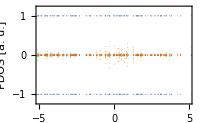

```mathematica
(* preview if neccessary *)
ListPlot[{predos1up,predos1dn,predos2up,predos2dn,predos3up,predos3dn,predos4up,predos4dn},PlotRange->{{-5,5},{-1.2,1.2}},FrameLabel->{"E - E_F [eV]","PDOS [a. u.]"},Frame->True,FrameStyle->Directive[Black,Thin,6],ImageSize->200,PlotStyle->Table[Directive[ColorData[97,"ColorList"][[Quotient[i,2]]]],{i,2,20}]]
```

```mathematica
(* Definitions *)
```

```mathematica
doublestyle={Directive[PointSize[Medium],Darker[Orange,.0]],Directive[PointSize[Medium],Darker[Orange,.1]],Directive[PointSize[Medium],Darker[Orange,.2]],Directive[PointSize[Medium],Darker[Orange,.3]],Directive[PointSize[Medium],Darker[Blue,.0]],Directive[PointSize[Medium],Darker[Blue,.1]],Directive[PointSize[Medium],Darker[Blue,.2]],Directive[PointSize[Medium],Darker[Blue,.3]],Directive[PointSize[Medium],Darker[Blue,.4]],Directive[PointSize[Medium],Darker[Red,.0]],Directive[PointSize[Medium],Darker[Green,.0]],Directive[PointSize[Medium],Darker[Green,.1]],Directive[PointSize[Medium],Darker[Green,.2]],Directive[PointSize[Medium],Darker[Green,.3]],Directive[PointSize[Medium],Darker[Green,.4]],Directive[PointSize[Medium],Darker[Red,.4]]};
```

```mathematica
doublestyle=Table[Directive[PointSize[Medium],ColorData[97,"ColorList"][[Quotient[i,2]]]],{i,2,20}];
```

```mathematica
doublestyle=Table[Directive[PointSize[Medium],ColorData[90,"ColorList"][[Quotient[i,2]]]],{i,2,20}];
```

```mathematica
colordata={Red,Black,Blue,Orange,White};
doublestyle=Table[Directive[PointSize[Medium],colordata[[Quotient[i,2]]]],{i,2,10}];
```

```mathematica
(* Now the real plotting *)
```

```mathematica
(* Big XY points plot *)
range=1.2*10^0;
jj=ListPlot[{predos1up,predos1dn,predos2up,predos2dn,predos3up,predos3dn,predos4up,predos4dn},Joined->False,PlotRange->{{-2,+2}(*{Automatic,Automatic}*),{-range,range}},PlotStyle->doublestyle (*PointSize[Medium]*)(*Directive[Black,PointSize[0.01]]*),Axes->{True,True},AxesStyle->AbsoluteThickness[2],AxesLabel->{,Style["Fermi Level",20,Black]},AxesOrigin->{0,0},Frame->True,FrameLabel->{"E - E_F [eV]"(*" E [eV]"*),"PDOS [a. u.]"},FrameStyle->Directive[Black,AbsoluteThickness[2],20],ImageSize->1500,Filling->(*{1->0}*)None,FillingStyle->Directive[Darker[Gray,.3],Opacity[.5]],AspectRatio->1/4,PlotLegends->Placed[LineLegend[{"Legend 1",None,"Legend 2",None,"Legend 3",None,"Legend 4",None,"Legend 5",None,"Legend 6".1c},LegendLabel->None(*"Legend:"*)(*"NEB image no.:"*),LabelStyle->{Darker[Gray,0.7],FontSize->32},LegendFunction->None],(*{0.75,0.75}*)Right]]
```

```mathematica
Export[path<>"states_spinpol.png",jj,Background->None]
```

/u/88/krejcio1/unix/WORK/1CLUSTERS/CSC2/3DGNR_double_mol_interatom/Reactions/NEB5/35/pdos_spinpol.png

CP2K continuous PDOS calculation

```mathematica
gaussian=True; (* smearing function -- Gaussian or Lorentzian *)
eta=0.05; (* eta=sigma=standard deviation [eV] ;*)dE=eta/2 (*normally at least eta/2, otherwise in [eV] *);
minE=-5;maxE=+5;

f[e_,ei_]:=If [gaussian,If[Abs[e-ei]>20eta,0,Exp[-((e-ei)^2)/(2eta^2)]/Sqrt[2 Pi eta^2]],1/(2Pi)*eta/((e-ei)^2+ 0.25*eta^2)];
dosup1=Table[{e,Sum[f[e,predos1up[[i,1]]]*predos1up[[i,2]],{i,Range[1,Length[predos1up]]}]},{e,minE,maxE,dE}];
dosdn1=Table[{e,Sum[f[e,predos1dn[[i,1]]]*predos1dn[[i,2]],{i,Range[1,Length[predos1dn]]}]},{e,minE,maxE,dE}];

dosup2=Table[{e,Sum[f[e,predos2up[[i,1]]]*predos2up[[i,2]],{i,Range[1,Length[predos2up]]}]},{e,minE,maxE,dE}];
dosdn2=Table[{e,Sum[f[e,predos2dn[[i,1]]]*predos2dn[[i,2]],{i,Range[1,Length[predos2dn]]}]},{e,minE,maxE,dE}];

dosup3=Table[{e,Sum[f[e,predos3up[[i,1]]]*predos3up[[i,2]],{i,Range[1,Length[predos3up]]}]},{e,minE,maxE,dE}];
dosdn3=Table[{e,Sum[f[e,predos3dn[[i,1]]]*predos3dn[[i,2]],{i,Range[1,Length[predos3dn]]}]},{e,minE,maxE,dE}];

dosup4=Table[{e,Sum[f[e,predos4up[[i,1]]]*predos4up[[i,2]],{i,Range[1,Length[predos4up]]}]},{e,minE,maxE,dE}];
dosdn4=Table[{e,Sum[f[e,predos4dn[[i,1]]]*predos4dn[[i,2]],{i,Range[1,Length[predos4dn]]}]},{e,minE,maxE,dE}];
```

```mathematica
(*rescalling of the PDOS per amount of atoms *)
dosup1[[All,2]]*=1/na1;
dosdn1[[All,2]]*=1/na1;

dosup2[[All,2]]*=1/na2;
dosdn2[[All,2]]*=1/na2;

dosup3[[All,2]]*=1/na3;
dosdn3[[All,2]]*=1/na3;

(*dosup4[[All,2]]*=1/na4;
dosdn4[[All,2]]*=1/na4;*)
```

## Plotting

```mathematica
(* Definitions *)
```

```mathematica
doublestyle={Directive[Thick,Darker[Orange,.0]],Directive[Thick,Darker[Orange,.1]],Directive[Thick,Darker[Orange,.2]],Directive[Thick,Darker[Orange,.3]],Directive[Thick,Darker[Blue,.0]],Directive[Thick,Darker[Blue,.1]],Directive[Thick,Darker[Blue,.2]],Directive[Thick,Darker[Blue,.3]],Directive[Thick,Darker[Blue,.4]],Directive[Thick,Darker[Red,.0]],Directive[Thick,Darker[Green,.0]],Directive[Thick,Darker[Green,.1]],Directive[Thick,Darker[Green,.2]],Directive[Thick,Darker[Green,.3]],Directive[Thick,Darker[Green,.4]],Directive[Thick,Darker[Red,.4]]};
```

```mathematica
doublestyle=Table[Directive[Thick,ColorData[97,"ColorList"][[Quotient[i,2]]]],{i,2,20}];
```

```mathematica
doublestyle=Table[Directive[Thick,ColorData[90,"ColorList"][[Quotient[i,2]]]],{i,2,20}];
```

```mathematica
colordata={Red,Black,Blue,Orange,White};
doublestyle=Table[Directive[Thick,colordata[[Quotient[i,2]]]],{i,2,10}];
```

```mathematica
(* Now the real plotting *)
```

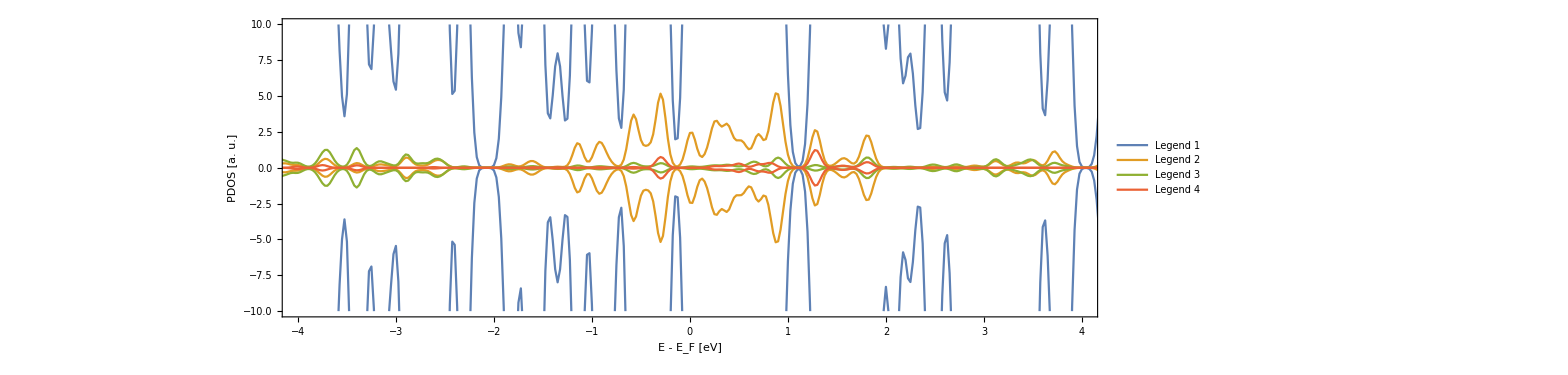

```mathematica
range=10;
jj=ListPlot[{dosup1,dosdn1,dosup2,dosdn2,dosup3,dosdn3,dosup4,dosdn4},Joined->True,PlotRange->{{-4,4},{-range,range}},PlotStyle->doublestyle,Axes->{True,True},AxesStyle->AbsoluteThickness[2],AxesLabel->{,Style["Fermi Level",20,Black]},AxesOrigin->{0,0},Frame->True,FrameLabel->{"E - E_F [eV]"(*" E [eV]"*),"PDOS [a. u.]"},FrameStyle->Directive[Black,AbsoluteThickness[2],20],ImageSize->1500,AspectRatio->1/4,PlotLegends->Placed[LineLegend[{"Legend 1",None,"Legend 2",None,"Legend 3",None,"Legend 4"},LegendLabel->None,LabelStyle->{Darker[Gray,0.7],FontSize->20},LegendFunction->None],(*{.66-0.24,.69+0.15}*)Right]]
```

```mathematica
Export[path<>"pdos_spinpol.png",jj,Background->None]
```

/u/88/krejcio1/unix/WORK/1CLUSTERS/CSC2/3DGNR_double_mol_interatom/Reactions/NEB5/35/pdos_spinpol.png

## VASP spin-orbit coupling

Here, the whole reading take much much longer, therefore it is better to read each directory or list of atoms differently and then assign the DOS to variables once it is completely read.
If necessary, adjust summing of doses... according to used LORBIT via un/commenting.

```mathematica
list=(*Table[i,{i,1,57,1}];*){1};
pathse=(*path;*)"~/Documents/WORK/z-sshfs/Tarkil/CuPc_SnSi/PBE+U_VASP_so/";
doscar1=Import[pathse<>"DOSCAR","Table"];
doscar1[[Range[1,7]]];
noat=doscar1[[1,1]];
nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];
fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
(*For[i=1,i≤noat,i++,{
dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,1,0,0,0,1,0,0,0,1,0,0}}],dosesmi[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,0,1,0,0,0,1,0,0,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,0,0,1,0,0,0,1,0,0,0,1}}],
dosesall[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,0,0,1,0,0,0,1,0,0,0}}],dos01[i]=.}];*)(* spd division only LORBIT=10*)
For[i=1,i≤noat,i++,{
dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
dos01[i].{0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0}}],
dosesmi[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
dos01[i].{0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
dos01[i].{0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1}}],
dosesall[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
dos01[i].{0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0}}],dos01[i]=.}]; (* spxpy... division - LORBIT = 11*)
dosesmolup=Array[Null,{nosteps,2}];
dosesmolup[[All,1]]=dostot[[All,1]];
dosesmoldn=Array[Null,{nosteps,2}];
dosesmoldn[[All,1]]=dostot[[All,1]];
dosesmolmi=Array[Null,{nosteps,2}];
dosesmolmi[[All,1]]=dostot[[All,1]];
dosesmolall=Array[Null,{nosteps,2}];
dosesmolall[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmolup[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolup[[i,2]]=dosesmolup[[i,2]]+dosesup[list[[j]]][[i,2]]],dosesmoldn[[i,2]]=0,
dosesmolmi[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolmi[[i,2]]=dosesmolmi[[i,2]]+dosesmi[list[[j]]][[i,2]]],
dosesmoldn[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmoldn[[i,2]]=dosesmoldn[[i,2]]+dosesdn[list[[j]]][[i,2]]],
dosesmolall[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolall[[i,2]]=dosesmolall[[i,2]]+dosesall[list[[j]]][[i,2]]]}];
(*fermi=Import[pathse<>"fermi.dat"][[1,3]]*)
dosesmolup2=Inner[Plus,dosesmolup,{-fermi+0,0},List];
dosesmolmi2=Inner[Plus,dosesmolmi,{-fermi+0,0},List];
dosesmoldn2=Inner[Plus,dosesmoldn,{-fermi+0,0},List];
dosesmolall2=Inner[Plus,dosesmolall,{-fermi+0,0},List];
dosesmolup2[[1,2]]=dosesmolup2[[2,2]];
dosesmolmi2[[1,2]]=dosesmolmi2[[2,2]];
dosesmoldn2[[1,2]]=dosesmoldn2[[2,2]];
dosesmolall2[[1,2]]=dosesmolall2[[2,2]];
```

-4.07159

```mathematica
(* Here follows the assigning to plottable variables *)
```

```mathematica
dosup1=dosesmolup2;dosmi1=dosesmolmi2;dosdn1=dosesmoldn2;dosall1=dosesmolall2;
```

```mathematica
dosup2=dosesmolup2;dosmi2=dosesmolmi2;dosdn2=dosesmoldn2;dosall2=dosesmolall2;
```

```mathematica
dosup3=dosesmolup2;dosmi3=dosesmolmi2;dosdn3=dosesmoldn2;dosall3=dosesmolall2;
```

```mathematica
dosup4=dosesmolup2;dosmi4=dosesmolmi2;dosdn4=dosesmoldn2;dosall4=dosesmolall2;
```

```mathematica
(* For possible shifting of the Fermi Level *)
shift=-0.150
dosup1[[All,1]]+=shift;
dosmi1[[All,1]]+=shift;
dosdn1[[All,1]]+=shift;
dosall1[[All,1]]+=shift;

(*dosup2[[All,1]]+=shift;
dosmi2[[All,1]]+=shift;
dosdn2[[All,1]]+=shift;
dosall2[[All,1]]+=shift;

dosup3[[All,1]]+=shift;
dosmi3[[All,1]]+=shift;
dosdn3[[All,1]]+=shift;
dosall3[[All,1]]+=shift;

dosup4[[All,1]]+=shift;
dosmi4[[All,1]]+=shift;
dosdn4[[All,1]]+=shift;
dosall4[[All,1]]+=shift;*)
```

-0.15

## Plotting: Spin-orbit coupling

```mathematica
(* Definitions *)
```

```mathematica
sostyle=Table[Directive[Thick,ColorData[97,"ColorList"][[Quotient[i,3]]]],{i,3,3*10}];
```

```mathematica
colordata={Red,Green,Blue,Orange};
sostyle=Table[Directive[Thick,colordata[[i]]],{i,Length[colordata]}];
```

```mathematica
sostyle={Thick,Thick,Thick,Thick,Directive[Thick,Dashed,ColorData[97][1]],Directive[Thick,Dashed,ColorData[97][2]],Directive[Thick,Dashed,ColorData[97][3]],Directive[Thick,Dashed,ColorData[97][4]]};
```

```mathematica
(* Now the real plotting *)
```

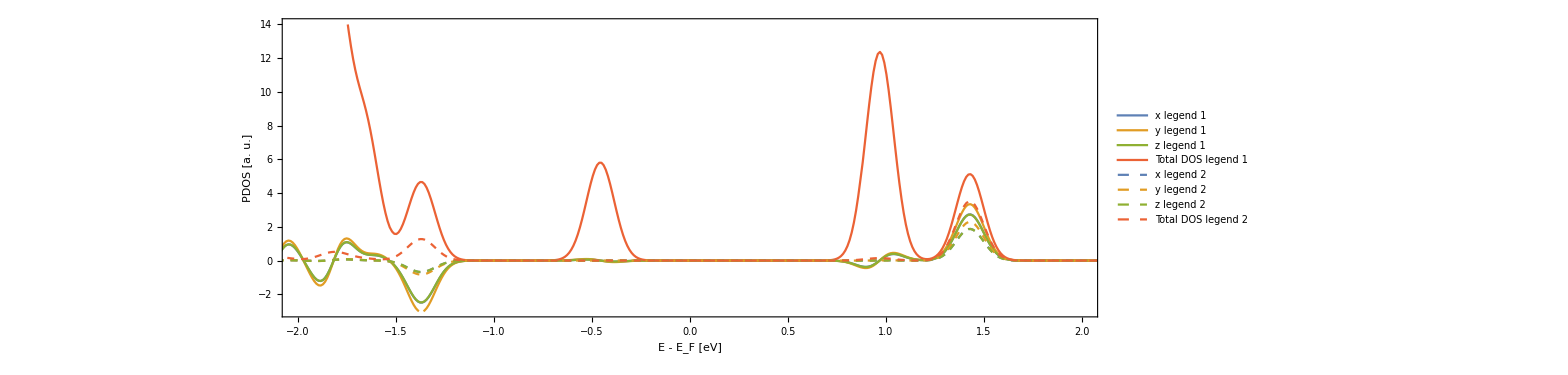

```mathematica
rangedn=3.;rangeup=14.;
jj=ListPlot[{dosup1,dosmi1,dosdn1,dosall1,dosup2,dosmi2,dosdn2,dosall2},Joined->True,PlotRange->{{-2,2},{-rangedn,rangeup}},PlotStyle->sostyle,Axes->{True,True},AxesStyle->AbsoluteThickness[2],AxesLabel->{,Style["Fermi Level",20,Black]},AxesOrigin->{0,0},Frame->True,FrameLabel->{"E - E_F [eV]"(*" E [eV]"*),"PDOS [a. u.]"},FrameStyle->Directive[Black,AbsoluteThickness[2],20],ImageSize->1500,AspectRatio->1/4,PlotLegends->Placed[LineLegend[{"x legend 1","y legend 1","z legend 1","Total DOS legend 1","x legend 2","y legend 2","z legend 2","Total DOS legend 2","x legend 3","y legend 3","z legend 3","Total DOS legend 3","x legend 4","y legend 4","z legend 4","Total DOS legend 4"},LegendLabel->None,LabelStyle->{Darker[Gray,0.7],FontSize->20},LegendFunction->None],(*{.66-0.24,.69+0.15}*)Right]]
```

```mathematica
Export[path<>"dos_spin-orbit.png",jj,Background->None]
```

## Mouse tracking

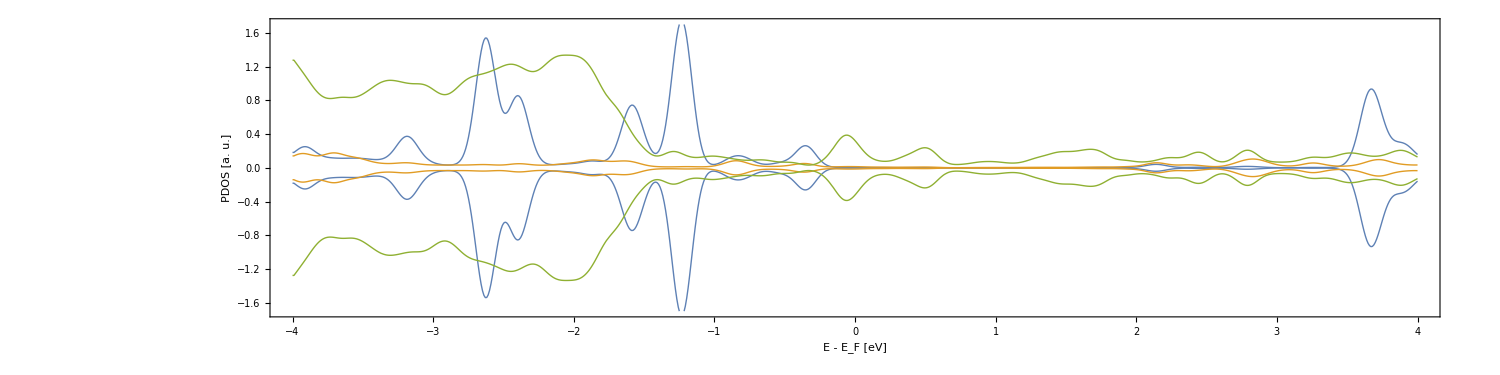
```mathematica
{-Graphics-,Dynamic[MousePosition["Graphics"]]}
```

{-Graphics-,}

## View

```mathematica
(* Note: For CP2K the following state view is way faster -- it has much less precalculations *)
```

```mathematica
atomicprop=Import[NotebookDirectory[]<>"/atomic_prop.dat","Table"];
(*path="~/Documents/WORK/z-sshfs/tmp/VASP/";*)
filename="input.xyz"; (* "bas","xyz","in" and CONTCAR/POSCAR files are supported at the moment *)
geomin= Import[path<>filename,"Table"];
geomin[[Range[1,20]]]//TableForm (* Just to see an example *)
```

51 |  |  |  | 
Lattice="19.014 0.0 0.0 9.507 16.4666070276 0.0 7.54627357635e-16 4.35684308068e-16 12.324" | Properties=species:S:1:pos:R:3:Z:I:1 | pbc="F F F" |  | 
Mo | 1.585 | 0.915 | 3.081 | 42
S | 3.169 | 1.83 | 1.516 | 16
S | 3.169 | 1.83 | 4.646 | 16
Mo | 3.1695 | 3.65943 | 3.081 | 42
S | 4.7535 | 4.57443 | 1.516 | 16
S | 4.7535 | 4.57443 | 4.646 | 16
Mo | 4.754 | 6.40387 | 3.081 | 42
S | 6.338 | 7.31887 | 1.516 | 16
S | 6.338 | 7.31887 | 4.646 | 16
Mo | 6.3385 | 9.1483 | 3.081 | 42
S | 7.9225 | 10.0633 | 1.516 | 16
S | 7.9225 | 10.0633 | 4.646 | 16
Mo | 7.923 | 11.8927 | 3.081 | 42
S | 9.507 | 12.8077 | 1.516 | 16
S | 9.507 | 12.8077 | 4.646 | 16
Mo | 9.5075 | 14.6372 | 3.081 | 42
Mo | 4.754 | 0.915 | 3.081 | 42
S | 6.338 | 1.83 | 1.516 | 16

```mathematica
(* geometry parser *)
If[StringTake[filename,-3]=="bas",{Print["BAS file"];maxat1=geomin[[1,1]];
geom=Array[Null,{maxat1,9}];
For[i=2,i≤maxat1+1,i++,geom[[i-1]]={geomin[[i,1]],atomicprop[[geomin[[i,1]],1]],geomin[[i,2]],geomin[[i,3]],geomin[[i,4]],atomicprop[[geomin[[i,1]],2]],atomicprop[[geomin[[i,1]],4]],atomicprop[[geomin[[i,1]],5]],atomicprop[[geomin[[i,1]],6]];}];};,
If[StringTake[filename,-3]=="xyz",{Print["XYZ file"];maxat1=geomin[[1,1]];
geom=Array[Null,{maxat1,9}];
For[i=3,i≤maxat1+2,i++,For[j=1,j≤99,j++,If[ToString[geomin[[i,1]]]==ToString[atomicprop[[j,1]]],geom[[i-2]]={j,geomin[[i,1]],geomin[[i,2]],geomin[[i,3]],geomin[[i,4]],atomicprop[[j,2]],atomicprop[[j,4]],atomicprop[[j,5]],atomicprop[[j,6]]};]]];};,
If[StringTake[filename,-3]==".in",{Print["FHI-AIMS in file"];aimsimport2=Array[Null,Length[geomin]];ia=1;cell={};
For[i=1,i≤Length[aimsimport2],i++,If[geomin[[i,1]]=="atom",{aimsimport2[[ia]]=geomin[[i]],ia=ia+1},If[geomin[[i,1]]=="lattice_vector",cell=Append[cell,geomin[[i,{2,3,4}]]]]]];
aimsimport2=Drop[aimsimport2,-Length[geomin]+ia-1];If[cell=={},cell=.];
xyzEx=aimsimport2[[All,{5,2,3,4}]];(*geomin=.;*)aimsimport2=.;
maxat1=Length[xyzEx];
geom=Array[Null,{maxat1,9}];
For[i=1,i≤maxat1,i++,For[j=1,j≤Length[atomicprop],j++,If[ToString[xyzEx[[i,1]]]==ToString[atomicprop[[j,1]]],geom[[i]]={j,xyzEx[[i,1]],xyzEx[[i,2]],xyzEx[[i,3]],xyzEx[[i,4]],atomicprop[[j,2]],atomicprop[[j,4]],atomicprop[[j,5]],atomicprop[[j,6]]};]]];};,
If[StringTake[filename,-3]=="CAR",{Print["CONTCAR/POSCAR VASP file"],(*VASP CONTCAR file *)direct=False;
If[geomin[[8,1]]=="Direct",{Print[".1dOK"],tmpn=8,direct=True},If[geomin[[9,1]]=="Direct",{Print[".1dOK"],tmpn=9,direct=True},
If[geomin[[8,1]]=="Cartesian",{Print[".1dOK"],tmpn=8},If[geomin[[9,1]]=="Cartesian",{Print[".1dOK"],tmpn=9},
{Print["problem: geomin[[8,1] = "]<>geomin[[8,1]],Print["problem: geomin[[9,1] = "]<>geomin[[9,1]]}]]]];
tmpn;cell=geomin[[{3,4,5}]];elem=geomin[[6]];
elnum=Length[elem];elemdic=Table[,{i,elnum}];atnum=geomin[[7]];
maxat1=Sum[atnum[[i]],{i,elnum}];atsum=Table[Sum[atnum[[i]],{i,j}],{j,1,elnum}];
For[i=1,i≤elnum,i++,For[j=1,j≤99,j++,If[ToString[elem[[i]]]==ToString[atomicprop[[j,1]]],elemdic[[i]]=j]]];elemdic;
geom=Array[Null,{maxat1,9}];
For[i=1,i≤maxat1,i++,{For[j=1,j≤elnum,j++,If[i≤atsum[[j]],{tmp=j,Break[]}]],k=elemdic[[tmp]],geom[[i]]={k,elem[[tmp]],geomin[[i+tmpn,1]],geomin[[i+tmpn,2]],geomin[[i+tmpn,3]],atomicprop[[k,2]],atomicprop[[k,4]],atomicprop[[k,5]],atomicprop[[k,6]]};};];
If[direct,geom[[All,{3,4,5}]]=geom[[All,{3,4,5}]].cell];},{Print["Unknown Format"]}]]]];
```

XYZ file

```mathematica
(* CONTINUATION of geometry reading and plotting *)
rescale = 0.2;
balls=Table[Tooltip[{RGBColor[geom[[i,{7,8,9}]]/256],Sphere[geom[[i,{3,4,5}]],rescale*geom[[i,6]]]},{i,geom[[i,{2,3,4,5}]]}],{i,1,maxat1}];
resbond=1.2;bond=.1;

geom2 = Array[Null, {(maxat1^2), 12}];
k1 = 1;
For[i = 1, i ≤maxat1 , i++, For[j = 1, j < i, j++, If[Norm[geom[[i,{3,4,5}]]-geom[[j,{3,4,5}]]]<= (atomicprop[[geom[[i, 1]], 3]]*resbond + atomicprop[[geom[[j, 1]], 3]]*resbond), {geom2[[k1, {1,2,3,7,8,9}]] =geom[[i,{ 3,4,5,7,8,9}]], geom2[[k1, {4,5,6,10,11,12}]] =geom[[j,{ 3,4,5,7,8,9}]], k1 = k1 + 1}]]];
geom2=Drop[geom2,k1-1-(maxat1^2)];
sticks=Table[Tube[{geom2[[i,{1,2,3}]],geom2[[i,{4,5,6}]]},bond,VertexColors->{RGBColor[geom2[[i,{7,8,9}]]/256],RGBColor[geom2[[i,{10,11,12}]]/256]}],{i,1,Length[geom2],1}];
```

```mathematica
Graphics3D[{balls,sticks},Lighting->"Neutral",ViewPoint->20000. {0,-1,0.1},ImageSize-> 300,Axes->False,Boxed-> False,Background->None]
```

-Graphics3D-

VASP, CP2K & FHI-AIMS spin-polarized

```mathematica
(* VASP spin-polarized*)
list=Table[i,{i,1,maxat1,1}];
pathse=path;doscar1=Import[pathse<>"DOSCAR_g","Table"];
(*doscar1[[Range[1,7]]]*)noat=doscar1[[1,1]];nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
(*For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];*)(* spd division only LORBIT=10*)
For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];(* spdf division only LORBIT=10*)
(*For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];*)(* spxpy... division - LORBIT = 11*)
dosesmolup=Array[Null,{nosteps,2}];
dosesmolup[[All,1]]=dostot[[All,1]];
dosesmoldn=Array[Null,{nosteps,2}];
dosesmoldn[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmolup[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolup[[i,2]]=dosesmolup[[i,2]]+dosesup[list[[j]]][[i,2]]],dosesmoldn[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmoldn[[i,2]]=dosesmoldn[[i,2]]+dosesdn[list[[j]]][[i,2]]]}];
dosesmolup2=Inner[Plus,dosesmolup,{-fermi+0,0},List];
dosesmoldn2=Inner[Plus,dosesmoldn,{-fermi+0,0},List];
dosesmolup2[[1,2]]=dosesmolup2[[2,2]]; (* 1st energy is always wrong *)
dosesmoldn2[[1,2]]=dosesmoldn2[[2,2]];
dosup1=dosesmolup2;dosdn1=dosesmoldn2;
```

-0.774192

```mathematica
(* FHI-AIMS spin-polarized*)
shift=0.0;
list=Table[i,{i,1,maxat1,1}];
j=2;  (* All orbitals: j=2; s-orb.08: j=3; p-orb: j=4; d-orb: j=5;*)
path0=path;
tmp1=Import[path0<>"geometry.in","Table"];bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];tmp1=.; (* possible error: Part::partw: "Part [i,1] of ... does not exist.", it has no effect on functionality*)
tmp2=Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosdn1=tmp2[[All,{1,2}]];
tmp2=.;dosdn1[[All,2]]=0.0;null=Table[0.0,{i,Length[dosdn1]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}]
dosdn1[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dosesdn[i]=dd[i],dd[i]=.},{i,list}];
dosdn1[[All,2]]*=-1;
dosdn1=Inner[Plus,dosdn1,{shift,0},List];

tmp2=Import[path0<>"atom_proj_dos_spin_up"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosup1=tmp2[[All,{1,2}]];
tmp2=.;dosup1[[All,2]]=0.0;null=Table[0.0,{i,Length[dosdn1]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}];dosup1[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dosesup[i]=dd[i],dd[i]=.},{i,list}];
dosup1=Inner[Plus,dosup1,{shift,0},List];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
(* CP2K PDOS *)
calcName="n6_cut0_s0"; (*only the firt part of the name before "-dosfile ...". *)
list=Table[i,{i,1,maxat1,1}];  (* Takes loong time - lots of precalculations *)
gaussian=False; (* smearing function -- Gaussian or Lorentzian *)
eta=0.05; (* eta=sigma=standard deviation [eV] ;*)dE=eta/2 (*normally at least eta/2, otherwise in [eV] *);
minE=-5;maxE=+5;Hart2eV=27.2116;shift=0.0;
path0=path;(*""~/Documents/WORK/PDOS_test_CP2K/";*) 
orbs:=Range[4,len[i]](*All orbitals together*); (*{4}(*s*);*) (*{5}(*p or py -- depending on "COMPONETNS"*);*) (* ... *) 
tmp=Import[path0<>calcName<>"-dosfile-ALPHA_list"<>ToString[list[[1]]]<>"-1.pdos","Table"][[1]];Fermi=tmp[[Length[tmp]-1]]*Hart2eV;tmp=.;
Do[{dd[i]=Import[path0<>calcName<>"-dosfile-ALPHA_list"<>ToString[i]<>"-1.pdos","Table",HeaderLines->2];len[i]=Length[dd[i][[1]]];},{i,list}];
predos1up=dd[list[[1]]][[All,{2,3}]]*Hart2eV;predos1up[[All,1]]+=shift-Fermi;
predos1up[[All,2]]=Sum[Sum[dd[i][[All,ji]],{ji,orbs}],{i,list}];
Do[{predosesup[i]=Sum[dd[i][[All,ji]],{ji,orbs}];dd[i]=.;len[i]=.;},{i,list}];
tmp=Import[path0<>calcName<>"-dosfile-BETA_list"<>ToString[list[[1]]]<>"-1.pdos","Table"][[1]];Fermi=tmp[[Length[tmp]-1]]*Hart2eV;tmp=.;
Do[{dd[i]=Import[path0<>calcName<>"-dosfile-BETA_list"<>ToString[i]<>"-1.pdos","Table",HeaderLines->2];len[i]=Length[dd[i][[1]]];},{i,list}];
predos1dn=dd[list[[1]]][[All,{2,3}]]*Hart2eV;predos1dn[[All,1]]+=shift-Fermi;
predos1dn[[All,2]]=-1*Sum[Sum[dd[i][[All,ji]],{ji,orbs}],{i,list}];
Do[{predosesdn[i]=-1*Sum[dd[i][[All,ji]],{ji,orbs}];dd[i]=.;len[i]=.;},{i,list}];Print["Files imported and adjusted; DOS procedure follows.".1d];
Fermi=.;f[e_,ei_]:=If [gaussian,If[Abs[e-ei]>20eta,0,Exp[-((e-ei)^2)/(2eta^2)]/Sqrt[2 Pi eta^2]],1/(2Pi)*eta/((e-ei)^2+ 0.25*eta^2)];
dosup1=Table[{e,Sum[f[e,predos1up[[i,1]]]*predos1up[[i,2]],{i,Range[1,Length[predos1up]]}]},{e,minE,maxE,dE}];
Do[{dosesup[i]=Table[{e,Sum[f[e,predos1up[[l,1]]]*predosesup[i][[l]],{l,Range[1,Length[predos1up]]}]},{e,minE,maxE,dE}];},{i,list}];Print["up-spin DOS calculated.".1d];
dosdn1=Table[{e,Sum[f[e,predos1dn[[i,1]]]*predos1dn[[i,2]],{i,Range[1,Length[predos1dn]]}]},{e,minE,maxE,dE}];
Do[{dosesdn[i]=Table[{e,Sum[f[e,predos1dn[[l,1]]]*predosesdn[i][[l]],{l,Range[1,Length[predos1dn]]}]},{e,minE,maxE,dE}];},{i,list}];Print["down-spin DOS calculated; DONE!".1d];
```

Files imported and adjusted; DOS procedure follows. .1d

up-spin DOS calculated. .1d

down-spin DOS calculated; DONE! .1d

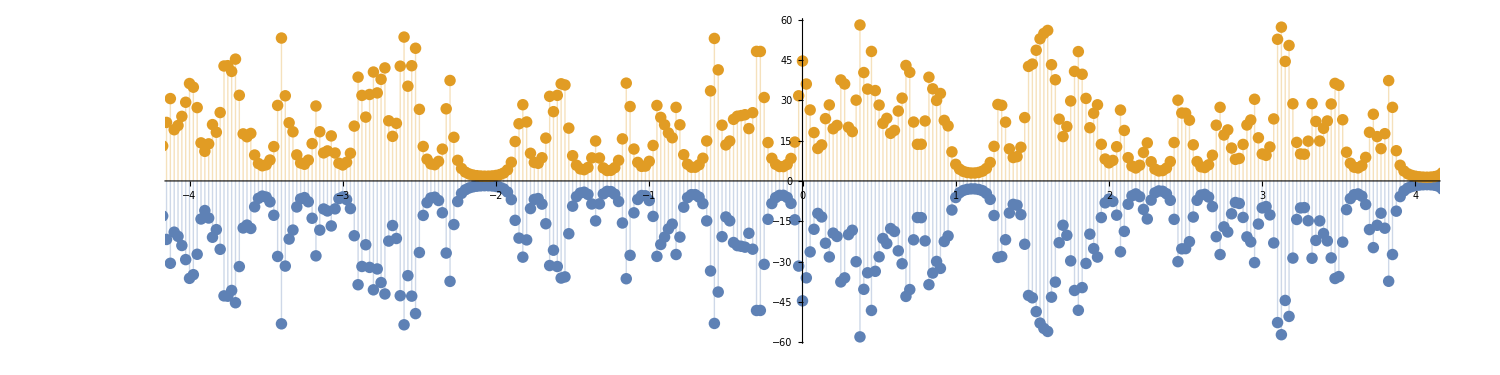

```mathematica
ListPlot[{Table[Tooltip[dosdn1[[i]],i],{i,1,Length[dosdn1]}],Table[Tooltip[dosup1[[i]],i],{i,1,Length[dosup1]}](*,{{-0.35,-200},{-0.35,+200}}*)(*for green guide to the eye*)},Filling->Axis,Joined->False,PlotRange->{{-4,4},{Min[dosdn1[[All,2]]],Max[dosup1[[All,2]]]}},ImageSize->1500,AspectRatio->1/4]
```

```mathematica
dosdn1[[365]] (* just to see the energy, to be absolutely sure *)
```

{-0.355808,-8.48524}

VASP spin-orbit coupling

```mathematica
(* VASP spin-orbit coupling*)
list=Table[i,{i,1,maxat1,1}];
pathse=path;
doscar1=Import[pathse<>"DOSCAR","Table"];
doscar1[[Range[1,7]]];
noat=doscar1[[1,1]];
nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];
fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
(*For[i=1,i≤noat,i++,{
dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,1,0,0,0,1,0,0,0,1,0,0}}],dosesmi[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,0,1,0,0,0,1,0,0,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,0,0,1,0,0,0,1,0,0,0,1}}],
dosesall[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,0,0,1,0,0,0,1,0,0,0}}],dos01[i]=.}];*) (* spd division only LORBIT=10*)
For[i=1,i≤noat,i++,{
dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
dos01[i].{0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0}}],
dosesmi[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
dos01[i].{0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
dos01[i].{0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1}}],
dosesall[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
dos01[i].{0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0}}],dos01[i]=.}]; (* spxpy... division - LORBIT = 11*)
dosesmolup=Array[Null,{nosteps,2}];
dosesmolup[[All,1]]=dostot[[All,1]];
dosesmoldn=Array[Null,{nosteps,2}];
dosesmoldn[[All,1]]=dostot[[All,1]];
dosesmolmi=Array[Null,{nosteps,2}];
dosesmolmi[[All,1]]=dostot[[All,1]];
dosesmolall=Array[Null,{nosteps,2}];
dosesmolall[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmolup[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolup[[i,2]]=dosesmolup[[i,2]]+dosesup[list[[j]]][[i,2]]],dosesmoldn[[i,2]]=0,
dosesmolmi[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolmi[[i,2]]=dosesmolmi[[i,2]]+dosesmi[list[[j]]][[i,2]]],
dosesmoldn[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmoldn[[i,2]]=dosesmoldn[[i,2]]+dosesdn[list[[j]]][[i,2]]],
dosesmolall[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolall[[i,2]]=dosesmolall[[i,2]]+dosesall[list[[j]]][[i,2]]]}];
(*fermi=Import[pathse<>"fermi.dat"][[1,3]]*)
dosesmolup2=Inner[Plus,dosesmolup,{-fermi+0,0},List];
dosesmolmi2=Inner[Plus,dosesmolmi,{-fermi+0,0},List];
dosesmoldn2=Inner[Plus,dosesmoldn,{-fermi+0,0},List];
dosesmolall2=Inner[Plus,dosesmolall,{-fermi+0,0},List];
dosesmolup2[[1,2]]=dosesmolup2[[2,2]];
dosesmolmi2[[1,2]]=dosesmolmi2[[2,2]];
dosesmoldn2[[1,2]]=dosesmoldn2[[2,2]];
dosesmolall2[[1,2]]=dosesmolall2[[2,2]];
```

-4.07159

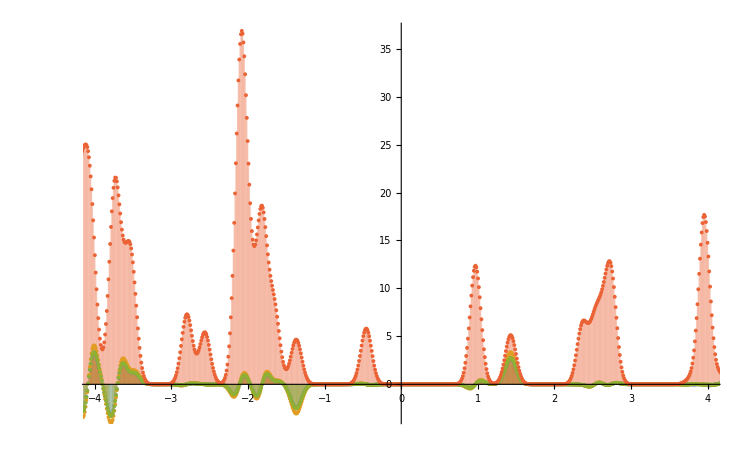

```mathematica
ListPlot[{Table[Tooltip[dosesmoldn2[[i]],i],{i,1,Length[dosesmoldn2]}],Table[Tooltip[dosesmolmi2[[i]],i],{i,1,Length[dosesmoldn2]}],Table[Tooltip[dosesmolup2[[i]],i],{i,1,Length[dosesmoldn2]}],Table[Tooltip[dosesmolall2[[i]],i],{i,1,Length[dosesmoldn2]}]},Filling->Axis,Joined->False,PlotRange->{{-4,4},{Min[dosesmoldn2[[All,2]]],Max[dosesmolall2[[All,2]]]}},ImageSize->750]
```

Visualization

```mathematica
type="sp";(*"so";*)  (* Type of calculations: "sp"=Spin-polarized; "so"=spin-orbit coupling *)
spin="all";(*"up";*)(*"down";*)(*"x";*)(*"y";*)(*"z";*)  (* Which spin to visualize *)
first=173;
last=195;
If[(spin=="up" )||( spin=="x"),{Do[{doses[i]=Abs[dosesup[i][[All,2]]]},{i,maxat1}],Print["up or x"]},If[(spin=="down") ||( spin=="z"),{Do[{doses[i]=Abs[dosesdn[i][[All,2]]]},{i,maxat1}],Print["down or z"]},If[( spin=="y"),{Do[{doses[i]=Abs[dosesmi[i][[All,2]]]},{i,maxat1}],Print["y"]},{(*spin=="all"*)Print["all"],If[type=="sp",{Do[{doses[i]=Abs[dosesup[i][[All,2]]]+Abs[dosesdn[i][[All,2]]]},{i,maxat1}],Print["sp"]},(*type=="so"*){Do[{doses[i]=Abs[dosesall[i][[All,2]]]},{i,maxat1}],Print["so"]}]}]]];
max=0.0;
For[i=1,i≤maxat1,i++,{dosessum[i]=Total[doses[i][[Range[first,last,1]]]],If[dosessum[i]>max,max=dosessum[i]]}];
max
For[i=1,i≤maxat1,i++,{dosessum[i]=dosessum[i]/max}]

rescale2 = 0.4;
color=(*"TemperatureMap"*)"DarkRainbow";
With[{c=ColorData[color]},
geom03=Table[{Opacity[dosessum[i]],(*Darker[Blue,.3]*)c[dosessum[i]],Sphere[geom[[i,{3,4,5}]],rescale2*geom[[i,6]]]},{i,1,maxat1}]];
expo=Graphics3D[{geom03,balls,sticks},Lighting->"Neutral",ViewPoint->20000. {0,-1,1},ImageSize->1000,Axes->False,Boxed-> False,Background->None]
```

all

sp

102.234

-Graphics3D-

```mathematica
Export[path<>"???_state.png",expo,Background->None]
```

```mathematica
expo=.
```

```mathematica
Do[{dosessum[i]=.;doses[i]=.},{i,maxat1}]
```

## CP2K states View

```mathematica
atomicprop=Import[NotebookDirectory[]<>"/atomic_prop.dat","Table"];
(*path="~/Documents/WORK/PDOS_test_CP2K_2_sp/";*)
filename="input.xyz"; (* "bas","xyz","in" and CONTCAR/POSCAR files are supported at the moment *)
geomin= Import[path<>filename,"Table"];
geomin[[Range[1,20]]]//TableForm (* Just to see an example *)
```

51 |  |  |  | 
Lattice="19.014 0.0 0.0 9.507 16.4666070276 0.0 7.54627357635e-16 4.35684308068e-16 12.324" | Properties=species:S:1:pos:R:3:Z:I:1 | pbc="F F F" |  | 
Mo | 1.585 | 0.915 | 3.081 | 42
S | 3.169 | 1.83 | 1.516 | 16
S | 3.169 | 1.83 | 4.646 | 16
Mo | 3.1695 | 3.65943 | 3.081 | 42
S | 4.7535 | 4.57443 | 1.516 | 16
S | 4.7535 | 4.57443 | 4.646 | 16
Mo | 4.754 | 6.40387 | 3.081 | 42
S | 6.338 | 7.31887 | 1.516 | 16
S | 6.338 | 7.31887 | 4.646 | 16
Mo | 6.3385 | 9.1483 | 3.081 | 42
S | 7.9225 | 10.0633 | 1.516 | 16
S | 7.9225 | 10.0633 | 4.646 | 16
Mo | 7.923 | 11.8927 | 3.081 | 42
S | 9.507 | 12.8077 | 1.516 | 16
S | 9.507 | 12.8077 | 4.646 | 16
Mo | 9.5075 | 14.6372 | 3.081 | 42
Mo | 4.754 | 0.915 | 3.081 | 42
S | 6.338 | 1.83 | 1.516 | 16

```mathematica
(* geometry parser *)
If[StringTake[filename,-3]=="bas",{Print["BAS file"];maxat1=geomin[[1,1]];
geom=Array[Null,{maxat1,9}];
For[i=2,i≤maxat1+1,i++,geom[[i-1]]={geomin[[i,1]],atomicprop[[geomin[[i,1]],1]],geomin[[i,2]],geomin[[i,3]],geomin[[i,4]],atomicprop[[geomin[[i,1]],2]],atomicprop[[geomin[[i,1]],4]],atomicprop[[geomin[[i,1]],5]],atomicprop[[geomin[[i,1]],6]];}];};,
If[StringTake[filename,-3]=="xyz",{Print["XYZ file"];maxat1=geomin[[1,1]];
geom=Array[Null,{maxat1,9}];
For[i=3,i≤maxat1+2,i++,For[j=1,j≤99,j++,If[ToString[geomin[[i,1]]]==ToString[atomicprop[[j,1]]],geom[[i-2]]={j,geomin[[i,1]],geomin[[i,2]],geomin[[i,3]],geomin[[i,4]],atomicprop[[j,2]],atomicprop[[j,4]],atomicprop[[j,5]],atomicprop[[j,6]]};]]];};,
If[StringTake[filename,-3]==".in",{Print["FHI-AIMS in file"];aimsimport2=Array[Null,Length[geomin]];ia=1;cell={};
For[i=1,i≤Length[aimsimport2],i++,If[geomin[[i,1]]=="atom",{aimsimport2[[ia]]=geomin[[i]],ia=ia+1},If[geomin[[i,1]]=="lattice_vector",cell=Append[cell,geomin[[i,{2,3,4}]]]]]];
aimsimport2=Drop[aimsimport2,-Length[geomin]+ia-1];If[cell=={},cell=.];
xyzEx=aimsimport2[[All,{5,2,3,4}]];(*geomin=.;*)aimsimport2=.;
maxat1=Length[xyzEx];
geom=Array[Null,{maxat1,9}];
For[i=1,i≤maxat1,i++,For[j=1,j≤Length[atomicprop],j++,If[ToString[xyzEx[[i,1]]]==ToString[atomicprop[[j,1]]],geom[[i]]={j,xyzEx[[i,1]],xyzEx[[i,2]],xyzEx[[i,3]],xyzEx[[i,4]],atomicprop[[j,2]],atomicprop[[j,4]],atomicprop[[j,5]],atomicprop[[j,6]]};]]];};,
If[StringTake[filename,-3]=="CAR",{Print["CONTCAR/POSCAR VASP file"],(*VASP CONTCAR file *)direct=False;
If[geomin[[8,1]]=="Direct",{Print[".1dOK"],tmpn=8,direct=True},If[geomin[[9,1]]=="Direct",{Print[".1dOK"],tmpn=9,direct=True},
If[geomin[[8,1]]=="Cartesian",{Print[".1dOK"],tmpn=8},If[geomin[[9,1]]=="Cartesian",{Print[".1dOK"],tmpn=9},
{Print["problem: geomin[[8,1] = "]<>geomin[[8,1]],Print["problem: geomin[[9,1] = "]<>geomin[[9,1]]}]]]];
tmpn;cell=geomin[[{3,4,5}]];elem=geomin[[6]];
elnum=Length[elem];elemdic=Table[,{i,elnum}];atnum=geomin[[7]];
maxat1=Sum[atnum[[i]],{i,elnum}];atsum=Table[Sum[atnum[[i]],{i,j}],{j,1,elnum}];
For[i=1,i≤elnum,i++,For[j=1,j≤99,j++,If[ToString[elem[[i]]]==ToString[atomicprop[[j,1]]],elemdic[[i]]=j]]];elemdic;
geom=Array[Null,{maxat1,9}];
For[i=1,i≤maxat1,i++,{For[j=1,j≤elnum,j++,If[i≤atsum[[j]],{tmp=j,Break[]}]],k=elemdic[[tmp]],geom[[i]]={k,elem[[tmp]],geomin[[i+tmpn,1]],geomin[[i+tmpn,2]],geomin[[i+tmpn,3]],atomicprop[[k,2]],atomicprop[[k,4]],atomicprop[[k,5]],atomicprop[[k,6]]};};];
If[direct,geom[[All,{3,4,5}]]=geom[[All,{3,4,5}]].cell];},{Print["Unknown Format"]}]]]].1c;
```

XYZ file

```mathematica
(* CONTINUATION of geometry reading and plotting *)
rescale = 0.2;
balls=Table[Tooltip[{RGBColor[geom[[i,{7,8,9}]]/256],Sphere[geom[[i,{3,4,5}]],rescale*geom[[i,6]]]},{i,geom[[i,{2,3,4,5}]]}],{i,1,maxat1}];
resbond=1.2;bond=.1;

geom2 = Array[Null, {(maxat1^2), 12}];
k1 = 1;
For[i = 1, i ≤maxat1 , i++, For[j = 1, j < i, j++, If[Norm[geom[[i,{3,4,5}]]-geom[[j,{3,4,5}]]]<= (atomicprop[[geom[[i, 1]], 3]]*resbond + atomicprop[[geom[[j, 1]], 3]]*resbond), {geom2[[k1, {1,2,3,7,8,9}]] =geom[[i,{ 3,4,5,7,8,9}]], geom2[[k1, {4,5,6,10,11,12}]] =geom[[j,{ 3,4,5,7,8,9}]], k1 = k1 + 1}]]];
geom2=Drop[geom2,k1-1-(maxat1^2)];
sticks=Table[Tube[{geom2[[i,{1,2,3}]],geom2[[i,{4,5,6}]]},bond,VertexColors->{RGBColor[geom2[[i,{7,8,9}]]/256],RGBColor[geom2[[i,{10,11,12}]]/256]}],{i,1,Length[geom2],1}];
```

```mathematica
Graphics3D[{balls,sticks},Lighting->"Neutral",ViewPoint->20000. {0,-1,0.1},ImageSize-> 300,Axes->False,Boxed-> False,Background->None]
```

-Graphics3D-

```mathematica
(* CP2K States *)
calcName="n6_cut0_s0"; (*only the firt part of the name before "-dosfile ...". *)
list=Table[i,{i,1,maxat1,1}];  (* Takes way shorter time - lots of precalculations *)
path0=path;(*""~/Documents/WORK/PDOS_test_CP2K/";*) Hart2eV=27.2116;shift=0.0;
orbs:=Range[4,len[i]](*All orbitals together*); (*{4}(*s*);*) (*{5}(*p or py -- depending on "COMPONETNS"*);*) (* ... *) 
tmp=Import[path0<>calcName<>"-dosfile-ALPHA_list"<>ToString[list[[1]]]<>"-1.pdos","Table"][[1]];Fermi=tmp[[Length[tmp]-1]]*Hart2eV;tmp=.;
Do[{dd[i]=Import[path0<>calcName<>"-dosfile-ALPHA_list"<>ToString[i]<>"-1.pdos","Table",HeaderLines->2];len[i]=Length[dd[i][[1]]];},{i,list}];
predos1up=dd[list[[1]]][[All,{2,3}]]*Hart2eV;predos1up[[All,1]]+=shift-Fermi;
predos1up[[All,2]]=Sum[Sum[dd[i][[All,ji]],{ji,orbs}],{i,list}];
Do[{predosesup[i]=Sum[dd[i][[All,ji]],{ji,orbs}];dd[i]=.;len[i]=.;},{i,list}];
tmp=Import[path0<>calcName<>"-dosfile-BETA_list"<>ToString[list[[1]]]<>"-1.pdos","Table"][[1]];Fermi=tmp[[Length[tmp]-1]]*Hart2eV;tmp=.;
Do[{dd[i]=Import[path0<>calcName<>"-dosfile-BETA_list"<>ToString[i]<>"-1.pdos","Table",HeaderLines->2];len[i]=Length[dd[i][[1]]];},{i,list}];
predos1dn=dd[list[[1]]][[All,{2,3}]]*Hart2eV;predos1dn[[All,1]]+=shift-Fermi;
predos1dn[[All,2]]=-1*Sum[Sum[dd[i][[All,ji]],{ji,orbs}],{i,list}];
Do[{predosesdn[i]=-1*Sum[dd[i][[All,ji]],{ji,orbs}];dd[i]=.;len[i]=.;},{i,list}];Print["Files imported and adjusted; DONE.".1d];
Fermi=.;
```

Files imported and adjusted; DONE. .1d

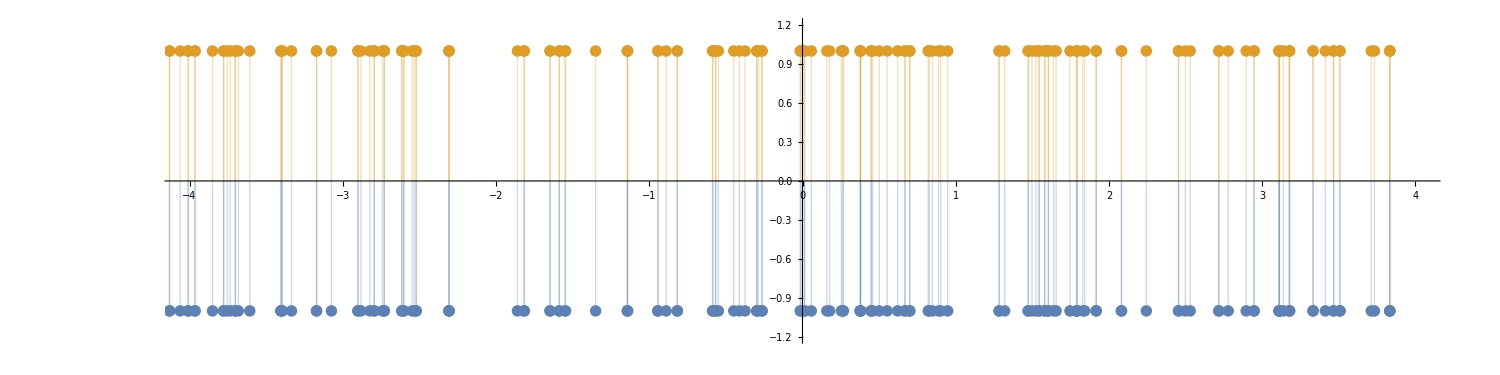

```mathematica
ListPlot[{Table[Tooltip[predos1dn[[i]],i],{i,1,Length[predos1dn]}],Table[Tooltip[predos1up[[i]],i],{i,1,Length[predos1up]}]},Filling->Axis,Joined->False,PlotRange->{{-4,4},{Min[predos1dn[[All,2]]]-0.2,Max[predos1up[[All,2]]]+0.2}},ImageSize->1500,AspectRatio->1/4]
```

```mathematica
first=240; (* Single or Multiple states *)
last=first (*200*);
spin="all";(*"up";*)(*"down";*)  (* Which spin to visualize *)
If[(spin=="up" )||( spin=="x"),{Do[{doses[i]=Abs[predosesup[i]]},{i,maxat1}],Print["up or x"]},If[(spin=="down") ||( spin=="z"),{Do[{doses[i]=Abs[predosesdn[i]]},{i,maxat1}],Print["down or z"]},{(*spin=="all"*){Do[{doses[i]=Abs[predosesup[i]]+Abs[predosesdn[i]]},{i,maxat1}],Print["all"]}}]];

max=0.0;
For[i=1,i≤maxat1,i++,{dosessum[i]=Total[doses[i][[Range[first,last,1]]]],If[dosessum[i]>max,max=dosessum[i]]}];
max
For[i=1,i≤maxat1,i++,{dosessum[i]=dosessum[i]/max}]

rescale2 = 0.4;
color=(*"TemperatureMap"*)"DarkRainbow";
With[{c=ColorData[color]},
geom03=Table[{Opacity[dosessum[i]],(*Darker[Blue,.3]*)c[dosessum[i]],Sphere[geom[[i,{3,4,5}]],rescale2*geom[[i,6]]]},{i,1,maxat1}]];
expo=Graphics3D[{geom03,balls,sticks},Lighting->"Neutral",ViewPoint->20000. {0,-1,1},ImageSize->1000,Axes->False,Boxed-> False,Background->None]
```

all

0.166238

-Graphics3D-

```mathematica
Export[path<>"-1.5_state.png",expo,Background->None]
```

Desktop/-4_state.png

```mathematica
expo=.
```

```mathematica
Do[{dosessum[i]=.;predosesup[i]=.;predosesdn[i]=.;doses[i]=.},{i,maxat1}]
```

## VASP states - PROCAR view

```mathematica
atomicprop=Import[NotebookDirectory[]<>"/atomic_prop.dat","Table"];
path="~/WORK/adam_nanoribbons/3_Au/";
filename="POSCAR"; (* "bas","xyz","in" and CONTCAR/POSCAR files are supported at the moment *)
geomin= Import[path<>filename,"Table"];
geomin[[Range[1,20]]]//TableForm (* Just to see an example *)
```

ini.xyz |  |  |  |  | 
1. |  |  |  |  | 
32.045941999999997 | 0. | 0. |  |  | 
-17.479679999999998 | 30.275690000000001 | 0. |  |  | 
0. | 0. | 26. |  |  | 
H | C | Au |  |  | 
36 | 144 | 660 |  |  | 
Selective | dynamics |  |  |  | 
Direct |  |  |  |  | 
0.484902 | 0.444879 | 0.859649 | T | T | T
0.389297 | 0.402103 | 0.8605 | T | T | T
0.313947 | 0.402221 | 0.860984 | T | T | T
0.265383 | 0.445336 | 0.859655 | T | T | T
0.487919 | 0.864901 | 0.861664 | T | T | T
0.498776 | 0.801548 | 0.861033 | T | T | T
0.507462 | 0.749325 | 0.859428 | T | T | T
0.192173 | 0.498795 | 0.857209 | T | T | T
0.175567 | 0.558903 | 0.857169 | T | T | T
0.155395 | 0.679725 | 0.860461 | T | T | T
0.165395 | 0.615699 | 0.859069 | T | T | T

```mathematica
(* geometry parser *)
If[StringTake[filename,-3]=="bas",{Print["BAS file"];maxat1=geomin[[1,1]];
geom=Array[Null,{maxat1,9}];
For[i=2,i≤maxat1+1,i++,geom[[i-1]]={geomin[[i,1]],atomicprop[[geomin[[i,1]],1]],geomin[[i,2]],geomin[[i,3]],geomin[[i,4]],atomicprop[[geomin[[i,1]],2]],atomicprop[[geomin[[i,1]],4]],atomicprop[[geomin[[i,1]],5]],atomicprop[[geomin[[i,1]],6]];}];};,
If[StringTake[filename,-3]=="xyz",{Print["XYZ file"];maxat1=geomin[[1,1]];
geom=Array[Null,{maxat1,9}];
For[i=3,i≤maxat1+2,i++,For[j=1,j≤99,j++,If[ToString[geomin[[i,1]]]==ToString[atomicprop[[j,1]]],geom[[i-2]]={j,geomin[[i,1]],geomin[[i,2]],geomin[[i,3]],geomin[[i,4]],atomicprop[[j,2]],atomicprop[[j,4]],atomicprop[[j,5]],atomicprop[[j,6]]};]]];};,
If[StringTake[filename,-3]==".in",{Print["FHI-AIMS in file"];aimsimport2=Array[Null,Length[geomin]];ia=1;cell={};
For[i=1,i≤Length[aimsimport2],i++,If[geomin[[i,1]]=="atom",{aimsimport2[[ia]]=geomin[[i]],ia=ia+1},If[geomin[[i,1]]=="lattice_vector",cell=Append[cell,geomin[[i,{2,3,4}]]]]]];
aimsimport2=Drop[aimsimport2,-Length[geomin]+ia-1];If[cell=={},cell=.];
xyzEx=aimsimport2[[All,{5,2,3,4}]];(*geomin=.;*)aimsimport2=.;
maxat1=Length[xyzEx];
geom=Array[Null,{maxat1,9}];
For[i=1,i≤maxat1,i++,For[j=1,j≤Length[atomicprop],j++,If[ToString[xyzEx[[i,1]]]==ToString[atomicprop[[j,1]]],geom[[i]]={j,xyzEx[[i,1]],xyzEx[[i,2]],xyzEx[[i,3]],xyzEx[[i,4]],atomicprop[[j,2]],atomicprop[[j,4]],atomicprop[[j,5]],atomicprop[[j,6]]};]]];};,
If[StringTake[filename,-3]=="CAR",{Print["CONTCAR/POSCAR VASP file"],(*VASP CONTCAR file *)direct=False;
If[geomin[[8,1]]=="Direct",{Print[".1dOK"],tmpn=8,direct=True},If[geomin[[9,1]]=="Direct",{Print[".1dOK"],tmpn=9,direct=True},
If[geomin[[8,1]]=="Cartesian",{Print[".1dOK"],tmpn=8},If[geomin[[9,1]]=="Cartesian",{Print[".1dOK"],tmpn=9},
{Print["problem: geomin[[8,1] = "]<>geomin[[8,1]],Print["problem: geomin[[9,1] = "]<>geomin[[9,1]]}]]]];
tmpn;cell=geomin[[{3,4,5}]];elem=geomin[[6]];
elnum=Length[elem];elemdic=Table[,{i,elnum}];atnum=geomin[[7]];
maxat1=Sum[atnum[[i]],{i,elnum}];atsum=Table[Sum[atnum[[i]],{i,j}],{j,1,elnum}];
For[i=1,i≤elnum,i++,For[j=1,j≤99,j++,If[ToString[elem[[i]]]==ToString[atomicprop[[j,1]]],elemdic[[i]]=j]]];elemdic;
geom=Array[Null,{maxat1,9}];
For[i=1,i≤maxat1,i++,{For[j=1,j≤elnum,j++,If[i≤atsum[[j]],{tmp=j,Break[]}]],k=elemdic[[tmp]],geom[[i]]={k,elem[[tmp]],geomin[[i+tmpn,1]],geomin[[i+tmpn,2]],geomin[[i+tmpn,3]],atomicprop[[k,2]],atomicprop[[k,4]],atomicprop[[k,5]],atomicprop[[k,6]]};};];
If[direct,geom[[All,{3,4,5}]]=geom[[All,{3,4,5}]].cell];},{Print["Unknown Format"]}]]]];
```

CONTCAR/POSCAR VASP file

.1dOK

```mathematica
maxat1=144+36
```

180

```mathematica
(* CONTINUATION of geometry reading and plotting *)
rescale = 0.2;
balls=Table[Tooltip[{RGBColor[geom[[i,{7,8,9}]]/256],Sphere[geom[[i,{3,4,5}]],rescale*geom[[i,6]]]},{i,geom[[i,{2,3,4,5}]]}],{i,1,maxat1}];
resbond=1.2;bond=.1;

geom2 = Array[Null, {(maxat1^2), 12}];
k1 = 1;
For[i = 1, i ≤maxat1 , i++, For[j = 1, j < i, j++, If[Norm[geom[[i,{3,4,5}]]-geom[[j,{3,4,5}]]]<= (atomicprop[[geom[[i, 1]], 3]]*resbond + atomicprop[[geom[[j, 1]], 3]]*resbond), {geom2[[k1, {1,2,3,7,8,9}]] =geom[[i,{ 3,4,5,7,8,9}]], geom2[[k1, {4,5,6,10,11,12}]] =geom[[j,{ 3,4,5,7,8,9}]], k1 = k1 + 1}]]];
geom2=Drop[geom2,k1-1-(maxat1^2)];
sticks=Table[Tube[{geom2[[i,{1,2,3}]],geom2[[i,{4,5,6}]]},bond,VertexColors->{RGBColor[geom2[[i,{7,8,9}]]/256],RGBColor[geom2[[i,{10,11,12}]]/256]}],{i,1,Length[geom2],1}];
```

```mathematica
Graphics3D[{balls,sticks},Lighting->"Neutral",ViewPoint->20000. {0,-0.1,0.1},ImageSize-> 300,Axes->False,Boxed-> False,Background->None]
```

-Graphics3D-

```mathematica
(* VASP spin-polarized*)
list=Table[i,{i,1,maxat1,1}];
pathse=path;procar=Import[pathse<>"PROCAR","Table"];
procar[[2]]
```

{#,of,k-points:,1,#,of,bands:,5148,#,of,ions:,840}

```mathematica
gaussian=False; (* smearing function -- Gaussian or Lorentzian *)
eta=0.05; (* eta=sigma=standard deviation [eV] ;*)dE=eta/2 (*normally at least eta/2, otherwise in [eV] *);
minE=-5;maxE=+5;shift=0.0;
```

```mathematica
nb=procar[[2,8]];noat=procar[[2,12]];l=Length[procar[[9]]]; (* 2 -- s; 3 -- p; 4 -- d ... Length[procar[[9]]]--total *);
bup=procar[[Range[6,(noat+5)*nb,noat+5],{5,8}]];
f[e_,ei_]:=If [gaussian,If[Abs[e-ei]>20eta,0,Exp[-((e-ei)^2)/(2eta^2)]/Sqrt[2 Pi eta^2]],1/(2Pi)*eta/((e-ei)^2+ 0.25*eta^2)];
```

```mathematica
(*doscar1[[Range[1,7]]]*)noat=doscar1[[1,1]];nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
(*For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];*)(* spd division only LORBIT=10*)
For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];(* spdf division only LORBIT=10*)
(*For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];*)(* spxpy... division - LORBIT = 11*)
dosesmolup=Array[Null,{nosteps,2}];
dosesmolup[[All,1]]=dostot[[All,1]];
dosesmoldn=Array[Null,{nosteps,2}];
dosesmoldn[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmolup[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolup[[i,2]]=dosesmolup[[i,2]]+dosesup[list[[j]]][[i,2]]],dosesmoldn[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmoldn[[i,2]]=dosesmoldn[[i,2]]+dosesdn[list[[j]]][[i,2]]]}];
dosesmolup2=Inner[Plus,dosesmolup,{-fermi+0,0},List];
dosesmoldn2=Inner[Plus,dosesmoldn,{-fermi+0,0},List];
dosesmolup2[[1,2]]=dosesmolup2[[2,2]]; (* 1st energy is always wrong *)
dosesmoldn2[[1,2]]=dosesmoldn2[[2,2]];
dosup1=dosesmolup2;dosdn1=dosesmoldn2;
```